## Мухамадиев Владимир

# Задание 7

## Загрузка и предварительная обработка

```mathematica
g1=Import[NotebookDirectory[]<>"//graph1.graphml"];
```

```mathematica
g2=Import[NotebookDirectory[]<>"//graph2.graphml"];
```

```mathematica
airports=SemanticImport[NotebookDirectory[]<>"//airports.dat"];
```

```mathematica
routes=SemanticImport[NotebookDirectory[]<>"//routes.dat"];
```

```mathematica
covdata=SemanticImport[NotebookDirectory[]<>"//covid_19_data.csv"];
```

```mathematica
tsc=SemanticImport[NotebookDirectory[]<>"//time_series_covid19_confirmed_global.csv"];
```

```mathematica
tsr=SemanticImport[NotebookDirectory[]<>"//time_series_covid19_recovered_global.csv"];
```

```mathematica
tsd=SemanticImport[NotebookDirectory[]<>"//time_series_covid19_deaths_global.csv"];
```

```mathematica
gdata=Import[NotebookDirectory[]<>"//g.m"];
```

```mathematica
gedata=Import[NotebookDirectory[]<>"//ge.m"];
```

```mathematica
erdata=Import[NotebookDirectory[]<>"//er.m"];
```

```mathematica
badata=Import[NotebookDirectory[]<>"//ba.m"];
```

```mathematica
sirdata=Import[NotebookDirectory[]<>"//sir.m"];
```

## Модели

```mathematica
NearestNeighborList[graph_]:=Module[{el=EdgeList[graph],vl=VertexList[graph],data={}},data=Sort[{Flatten[{el⟦All,1⟧,el⟦All,2⟧}],Flatten[{el⟦All,2⟧,el⟦All,1⟧}]}ᵀ];data=Table[Cases[data,{vl⟦i⟧,_}]⟦All,2⟧,{i,1,Length[vl]}];data]
```

### SI

```mathematica
SI[graph_,i0_,β_,t_]:=Module[{vc=VertexCount[graph],data={VertexList[graph],NearestNeighborList[graph],ConstantArray["Susceptible",VertexCount[graph]]}ᵀ,out=ConstantArray[{},t+1],iv={}},out⟦1⟧={vc-i0,i0};iv=RandomSample[Range[vc],i0];Do[data⟦iv⟦i⟧,3⟧="Infected",{i,1,i0}];Do[iv=Cases[data,{_,_,"Infected"}];Do[Do[If[RandomChoice[{β,1-β}->{True,False}]==True,data⟦FirstPosition[data,{iv⟦j,2,k⟧,_,_},Missing["NotFound"],1]⟦1⟧,3⟧="Infected"],{k,1,Length[iv⟦j,2⟧]}],{j,1,Length[iv]}];out⟦i⟧={Length[Cases[data,{_,_,"Susceptible"}]],Length[Cases[data,{_,_,"Infected"}]]},{i,2,t+1}];out={{Range[0,t],out⟦All,1⟧}ᵀ,{Range[0,t],out⟦All,2⟧}ᵀ};out]
```

### SIS

```mathematica
SIS[graph_,i0_,β_,μ_,t_]:=Module[{vc=VertexCount[graph],data={VertexList[graph],NearestNeighborList[graph],ConstantArray["Susceptible",VertexCount[graph]]}ᵀ,out=ConstantArray[{},t+1],iv={}},out⟦1⟧={vc-i0,i0};iv=RandomSample[Range[vc],i0];Do[data⟦iv⟦i⟧,3⟧="Infected",{i,1,i0}];Do[iv=Cases[data,{_,_,"Infected"}];Do[Do[If[RandomChoice[{β,1-β}->{True,False}]==True,data⟦FirstPosition[data,{iv⟦j,2,k⟧,_,_},Missing["NotFound"],1]⟦1⟧,3⟧="Infected"],{k,1,Length[iv⟦j,2⟧]}],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦FirstPosition[data⟦All,1⟧,iv⟦j,1⟧]⟦1⟧,3⟧="Susceptible"],{j,1,Length[iv]}];out⟦i⟧={Length[Cases[data,{_,_,"Susceptible"}]],Length[Cases[data,{_,_,"Infected"}]]},{i,2,t+1}];out={{Range[0,t],out⟦All,1⟧}ᵀ,{Range[0,t],out⟦All,2⟧}ᵀ};out]
```

### SIR

```mathematica
SIR[graph_,i0_,β_,μ_,t_]:=Module[{vc=VertexCount[graph],data={VertexList[graph],NearestNeighborList[graph],ConstantArray["Susceptible",VertexCount[graph]]}ᵀ,out=ConstantArray[{},t+1],iv={},pos=0},out⟦1⟧={vc-i0,i0,0};iv=RandomSample[Range[vc],i0];Do[data⟦iv⟦i⟧,3⟧="Infected",{i,1,i0}];Do[iv=Cases[data,{_,_,"Infected"}];Do[Do[If[RandomChoice[{β,1-β}->{True,False}]==True,pos=FirstPosition[data,{iv⟦j,2,k⟧,_,_},Missing["NotFound"],1]⟦1⟧;If[data⟦pos,3⟧=="Susceptible",data⟦pos,3⟧="Infected"]],{k,1,Length[iv⟦j,2⟧]}],{j,1,Length[iv]}];Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦FirstPosition[data⟦All,1⟧,iv⟦j,1⟧]⟦1⟧,3⟧="Recovered"],{j,1,Length[iv]}];out⟦i⟧={Length[Cases[data,{_,_,"Susceptible"}]],Length[Cases[data,{_,_,"Infected"}]],Length[Cases[data,{_,_,"Recovered"}]]},{i,2,t+1}];out={{Range[0,t],out⟦All,1⟧}ᵀ,{Range[0,t],out⟦All,2⟧}ᵀ,{Range[0,t],out⟦All,3⟧}ᵀ};out]
```

## 1. Влияние топологии на характерное время распространение эпидемии в SI модели

### Модель Эрдеша-Реньи

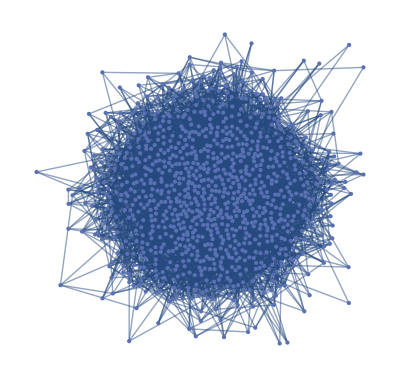

```mathematica
erg=gdata⟦1⟧(*erg=RandomGraph[{1000,5000}]*)
```

```mathematica
erge=gedata⟦1⟧;(*erge={Range[0,30],Divide[Mean[Table[SI[erg,10,0.05,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

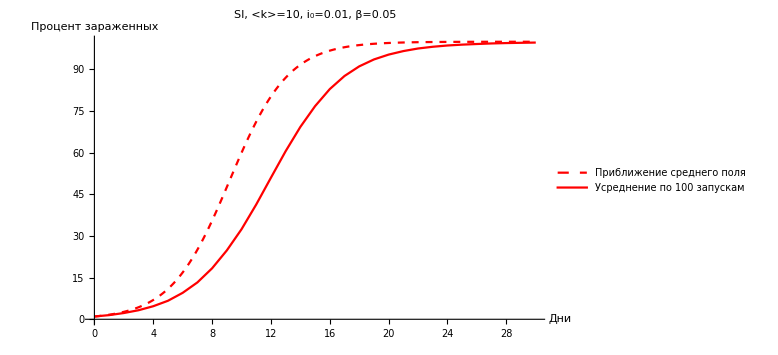

```mathematica
ListLinePlot[{Table[{t,100(0.01 ⅇ^(0.5t))/(0.99+0.01 ⅇ^(0.5t))},{t,0,30,0.1}],erge},PlotStyle->{Directive[Red,Dashed],Red},PlotLegends->Placed[{"Приближение среднего поля","Усреднение по 100 запускам"},Below],AxesLabel->{"Дни","Процент\nзараженных"},PlotLabel->"SI, <k>=10, i_0=0.01, β=0.05",ImageSize->Large]
```

### Модель Барабаши-Альберта

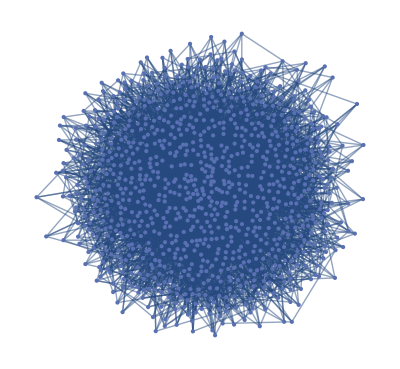

```mathematica
bag=gdata⟦2⟧(*bag=RandomGraph[BarabasiAlbertGraphDistribution[1000,5]]*)
```

```mathematica
bage=gedata⟦2⟧;(*bage={Range[0,30],Divide[Mean[Table[SI[bag,10,0.05,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

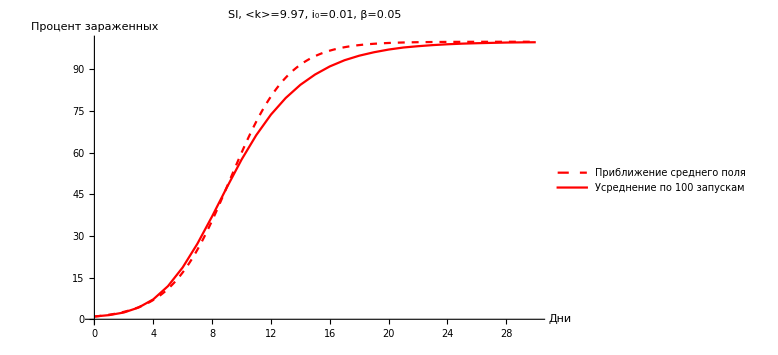

```mathematica
ListLinePlot[{Table[{t,100(0.01 ⅇ^(0.5t))/(0.99+0.01 ⅇ^(0.5t))},{t,0,30,0.1}],bage},PlotStyle->{Directive[Red,Dashed],Red},PlotLegends->Placed[{"Приближение среднего поля","Усреднение по 100 запускам"},Below],AxesLabel->{"Дни","Процент\nзараженных"},PlotLabel->"SI, <k>=9.97, i_0=0.01, β=0.05",ImageSize->Large]
```

### Модель Ваттса-Строгатца

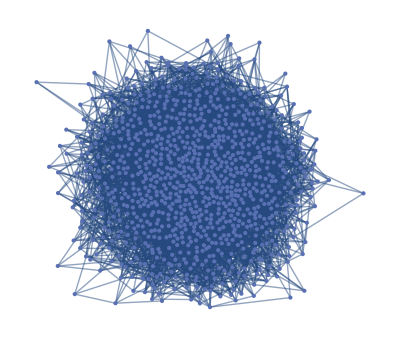

```mathematica
wsg1=gdata⟦3⟧(*wsg1=RandomGraph[WattsStrogatzGraphDistribution[1000,1,5]]*)
```

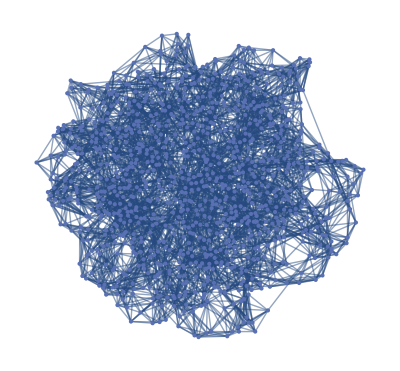

```mathematica
wsg0p1=gdata⟦4⟧(*wsg0p1=RandomGraph[WattsStrogatzGraphDistribution[1000,0.1,5]]*)
```

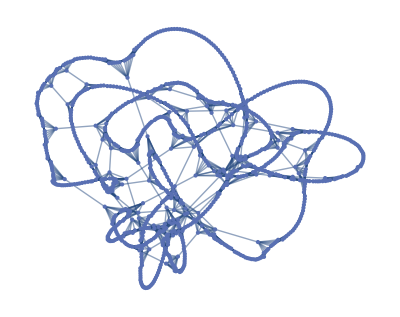

```mathematica
wsg0p01=gdata⟦5⟧(*wsg0p01=RandomGraph[WattsStrogatzGraphDistribution[1000,0.01,5]]*)
```

```mathematica
wsg1e=gedata⟦3⟧;(*wsg1e={Range[0,30],Divide[Mean[Table[SI[wsg1,10,0.05,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
wsg0p1e=gedata⟦4⟧;(*wsg0p1e={Range[0,30],Divide[Mean[Table[SI[wsg0p1,10,0.05,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
wsg0p01e=gedata⟦5⟧;(*wsg0p01e={Range[0,30],Divide[Mean[Table[SI[wsg0p01,10,0.05,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

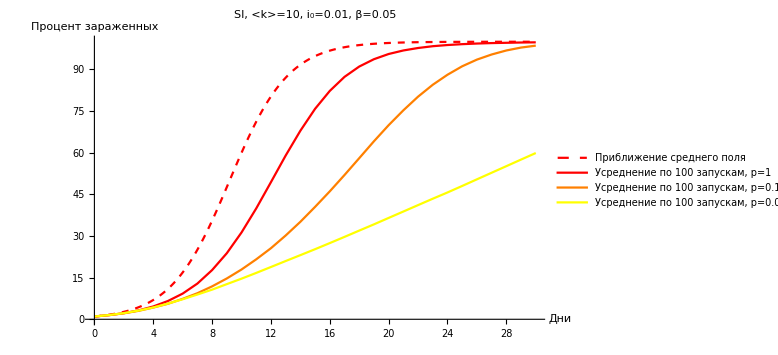

```mathematica
ListLinePlot[{Table[{t,100(0.01 ⅇ^(0.5t))/(0.99+0.01 ⅇ^(0.5t))},{t,0,30,0.1}],wsg1e,wsg0p1e,wsg0p01e},PlotStyle->{Directive[Red,Dashed],Red,Orange,Yellow},PlotLegends->Placed[{"Приближение среднего поля","Усреднение по 100 запускам, p=1","Усреднение по 100 запускам, p=0.1","Усреднение по 100 запускам, p=0.01"},Below],AxesLabel->{"Дни","Процент\nзараженных"},PlotLabel->"SI, <k>=10, i_0=0.01, β=0.05",ImageSize->Large]
```

## 2. Порог зажигания в модели SIS

### Модель Эрдеша-Реньи

```mathematica
ersis0p2=erdata⟦1⟧;(*ersis0p2={Range[0,30],Divide[Mean[Table[SIS[erg,10,0.2,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
ersis0p15=erdata⟦2⟧;(*ersis0p15={Range[0,30],Divide[Mean[Table[SIS[erg,10,0.15,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
ersis0p1=erdata⟦3⟧;(*ersis0p1={Range[0,30],Divide[Mean[Table[SIS[erg,10,0.1,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
ersis0p05=erdata⟦4⟧;(*ersis0p05={Range[0,30],Divide[Mean[Table[SIS[erg,10,0.05,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

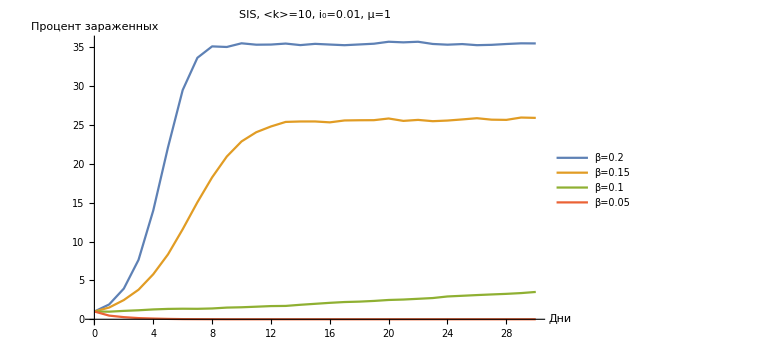

```mathematica
ListLinePlot[{ersis0p2,ersis0p15,ersis0p1,ersis0p05},AxesLabel->{"Дни","Процент\nзараженных"},PlotLegends->Placed[{"β=0.2","β=0.15","β=0.1","β=0.05"},Below],PlotLabel->"SIS, <k>=10, i_0=0.01, μ=1",ImageSize->Large]
```

### Модель Барабаши-Альберта

```mathematica
basis0p2=badata⟦1⟧;(*basis0p2={Range[0,30],Divide[Mean[Table[SIS[bag,10,0.2,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
basis0p15=badata⟦2⟧;(*basis0p15={Range[0,30],Divide[Mean[Table[SIS[bag,10,0.15,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
basis0p1=badata⟦3⟧;(*basis0p1={Range[0,30],Divide[Mean[Table[SIS[bag,10,0.1,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

```mathematica
basis0p05=badata⟦4⟧;(*basis0p05={Range[0,30],Divide[Mean[Table[SIS[bag,10,0.05,1,30]⟦2,All,2⟧,{l,1,100}]],10]}ᵀ;*)
```

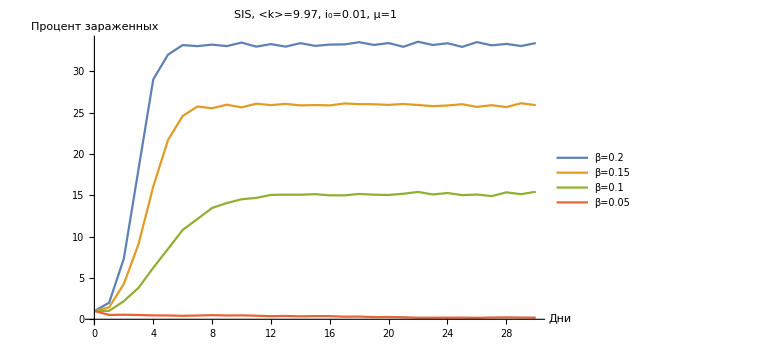

```mathematica
ListLinePlot[{basis0p2,basis0p15,basis0p1,basis0p05},AxesLabel->{"Дни","Процент\nзараженных"},PlotLegends->Placed[{"β=0.2","β=0.15","β=0.1","β=0.05"},Below],PlotLabel->"SIS, <k>=9.97, i_0=0.01, μ=1",ImageSize->Large]
```

## 3. Влияние топологии в модели SIR

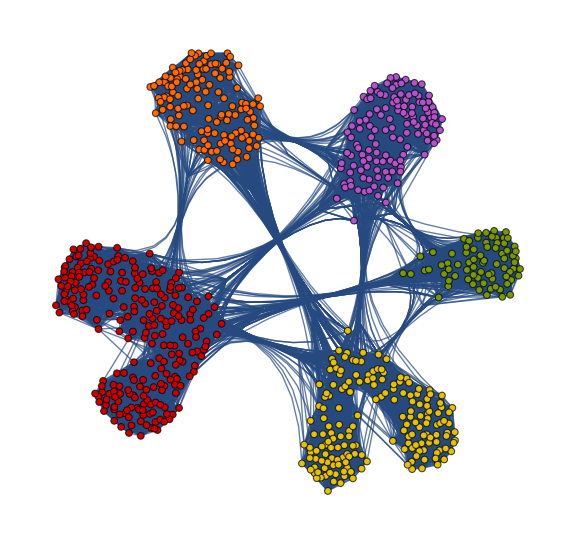

```mathematica
CommunityGraphPlot[g1,CommunityBoundaryStyle->None,ImageSize->Large]
```

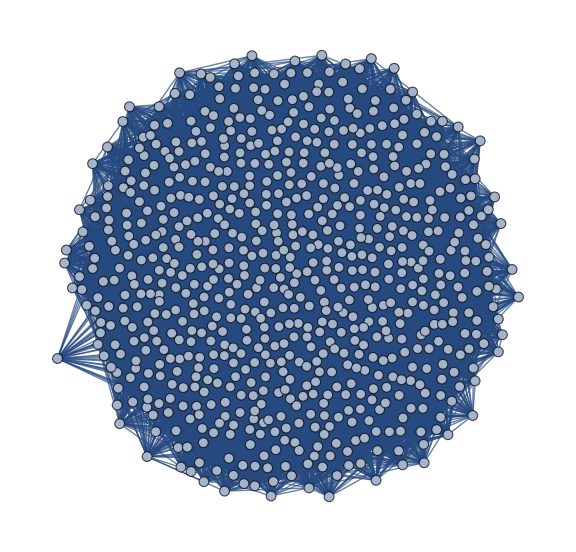

```mathematica
GraphPlot[g2,ImageSize->Large]
```

```mathematica
sirg1i1=sirdata⟦1⟧;
(*sirg1i1=Table[SIR[g1,1,0.005,0.03,200],{l,1,100}];
sirg1i1={{Range[0,200],Mean[sirg1i1⟦All,1,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg1i1⟦All,2,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg1i1⟦All,3,All,2⟧]}ᵀ};*)
```

```mathematica
sirg2i1=sirdata⟦2⟧;
(*sirg2i1=Table[SIR[g2,1,0.005,0.03,200],{l,1,100}];
sirg2i1={{Range[0,200],Mean[sirg2i1⟦All,1,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg2i1⟦All,2,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg2i1⟦All,3,All,2⟧]}ᵀ};*)
```

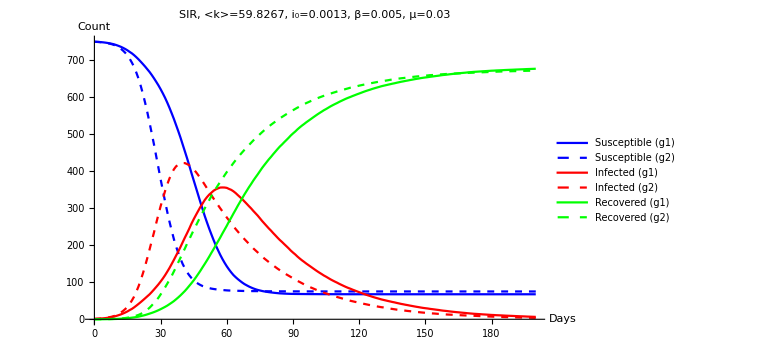

```mathematica
ListLinePlot[{sirg1i1⟦1⟧,sirg2i1⟦1⟧,sirg1i1⟦2⟧,sirg2i1⟦2⟧,sirg1i1⟦3⟧,sirg2i1⟦3⟧},PlotStyle->{Blue, Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed]},PlotLegends->Placed[{"Susceptible (g1)","Susceptible (g2)","Infected (g1)","Infected (g2)","Recovered (g1)","Recovered (g2)"},Below],AxesLabel->{"Days","Count"},PlotLabel->"SIR, <k>=59.8267, i_0=0.0013, β=0.005, μ=0.03",ImageSize->Large]
```

### Для сети раздробленной на большее число блоков будет более низкий пик по числу зараженных. Это нивелируется увеличением начального числа зараженных.

```mathematica
sirg1i50=sirdata⟦3⟧;
(*sirg1i50=Table[SIR[g1,50,0.005,0.03,200],{l,1,100}];
sirg1i50={{Range[0,200],Mean[sirg1i50⟦All,1,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg1i50⟦All,2,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg1i50⟦All,3,All,2⟧]}ᵀ};*)
```

```mathematica
sirg2i50=sirdata⟦4⟧;
(*sirg2i50=Table[SIR[g2,50,0.005,0.03,200],{l,1,100}];
sirg2i50={{Range[0,200],Mean[sirg2i50⟦All,1,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg2i50⟦All,2,All,2⟧]}ᵀ,{Range[0,200],Mean[sirg2i50⟦All,3,All,2⟧]}ᵀ};*)
```

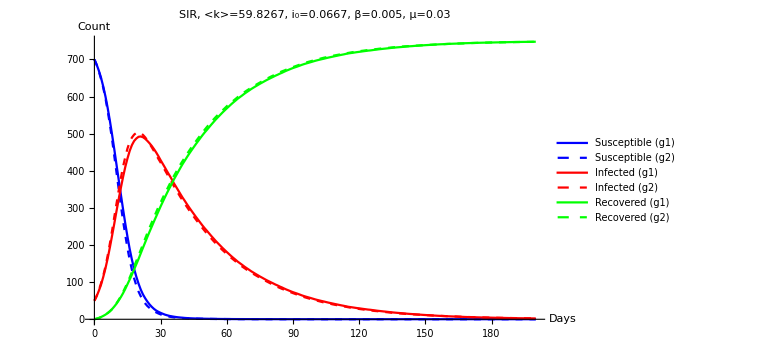

```mathematica
ListLinePlot[{sirg1i50⟦1⟧,sirg2i50⟦1⟧,sirg1i50⟦2⟧,sirg2i50⟦2⟧,sirg1i50⟦3⟧,sirg2i50⟦3⟧},PlotStyle->{Blue, Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed]},PlotLegends->Placed[{"Susceptible (g1)","Susceptible (g2)","Infected (g1)","Infected (g2)","Recovered (g1)","Recovered (g2)"},Below],AxesLabel->{"Days","Count"},PlotLabel->"SIR, <k>=59.8267, i_0=0.0667, β=0.005, μ=0.03",ImageSize->Large]
```

## 4. Моделирование распространения Covid-19

### По странам с числом выявленных случаев более 10000

```mathematica
c=tsc[Select[#⟦1⟧==""&]][Select[#⟦Dimensions[tsc]⟦2⟧⟧≥10000&]];
c=SortBy[Append[Replace[Table[{c[i,2],Select[Normal[Normal[c[i]]]⟦5;;-1,2⟧,#≥1000&]},{i,1,Length[c]}],Missing["Unrecognized","Korea, South"]->Entity["Country","SouthKorea"],2],{Entity["Country","China"],Select[Total[Normal[Normal[tsc[Select[#⟦2⟧==Entity["Country","China"]&]][All,5;;-1]]]⟦All,All,2⟧],#≥1000&]⟦1;;51⟧}],First];
c=Table[{c⟦i,1⟧,{Range[0,Length[c⟦i,2⟧]-1],c⟦i,2⟧}ᵀ},{i,1,Length[c]}];
```

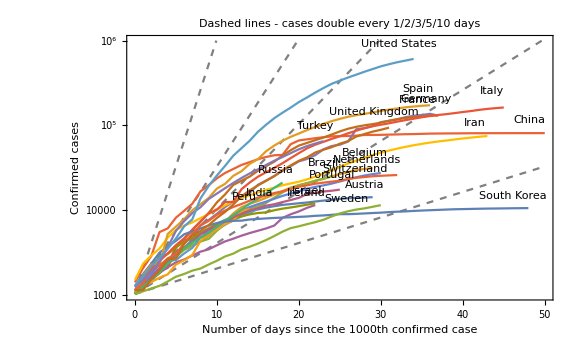

```mathematica
Show[LogPlot[{2^(k+10),2^(k/2+10),2^(k/3+10),2^(k/5+10),2^(k/10+10)},{k,0,50},PlotStyle->Directive[Gray,Dashed],Axes->False,Frame->{{True,False},{True,False}},GridLines->{{10,20,30,40,50},{10000,100000,1000000}},FrameTicks->{{0,10,20,30,40,50},{1000,10000,100000,1000000}},FrameLabel->{"Number of days since the 1000th confirmed case","Confirmed cases"},GridLinesStyle->Directive[Gray,Thin],PlotRange->{{0,50},{1000,1000000}}],ListLogPlot[c⟦All,2⟧,Joined->True,PlotLabels->Placed[c⟦All,1⟧,Above],PlotRange->{{0,50},{1000,1000000}}],PlotLabel->"Dashed lines - cases double every 1/2/3/5/10 days",ImageSize->Large]
```

### Модель SIRD

```mathematica
SIRDi[β_,μ_,σ_,s0_,i0_,r0_,d0_,t_]:=NestList[{#⟦1⟧(1-β#⟦2⟧),#⟦2⟧(1+β#⟦1⟧-μ-σ),#⟦3⟧+μ#⟦2⟧,#⟦4⟧+σ#⟦2⟧}&,{s0,i0,r0,d0},t-1]
```

### По провинции Хубэй

```mathematica
hubei=Normal[Normal[covdata[Select[#⟦3⟧=="Hubei"&]][All,6;;8]]];
```

```mathematica
hs0=(hubei⟦-1,1,2⟧-hubei⟦1,1,2⟧)/hubei⟦-1,1,2⟧;
```

```mathematica
hi0=(hubei⟦1,1,2⟧-hubei⟦1,2,2⟧-hubei⟦1,3,2⟧)/hubei⟦-1,1,2⟧;
```

```mathematica
hr0=hubei⟦1,3,2⟧/hubei⟦-1,1,2⟧;
```

```mathematica
hd0=hubei⟦1,2,2⟧/hubei⟦-1,1,2⟧;
```

#### Совпадение по пику зараженных

```mathematica
hv1=SIRDi[0.325,0.0325,0.002,hs0,hi0,hr0,hd0,Length[hubei]];
```

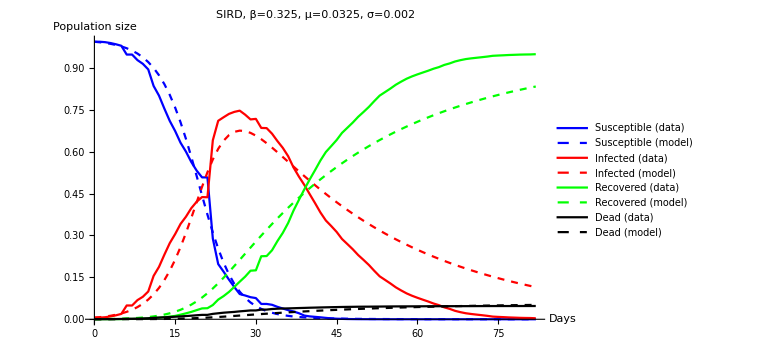

```mathematica
ListLinePlot[{{Range[0,Length[hubei]-1],(hubei⟦-1,1,2⟧-hubei⟦All,1,2⟧)/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv1⟦All,1⟧}ᵀ,{Range[0,Length[hubei]-1],(hubei⟦All,1,2⟧-hubei⟦All,2,2⟧-hubei⟦All,3,2⟧)/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv1⟦All,2⟧}ᵀ,{Range[0,Length[hubei]-1],hubei⟦All,3,2⟧/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv1⟦All,3⟧}ᵀ,{Range[0,Length[hubei]-1],hubei⟦All,2,2⟧/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv1⟦All,4⟧}ᵀ},PlotStyle->{Blue,Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed],Black,Directive[Black,Dashed]},PlotLegends->Placed[{"Susceptible (data)","Susceptible (model)","Infected (data)","Infected (model)","Recovered (data)","Recovered (model)","Dead (data)","Dead (model)"},Below],AxesLabel->{"Days","Population size"},PlotLabel->"SIRD, β=0.325, μ=0.0325, σ=0.002",ImageSize->Large]
```

#### Совпадение по времени окончания

```mathematica
hv2=SIRDi[0.6,0.06,0.003,hs0,hi0,hr0,hd0,Length[hubei]];
```

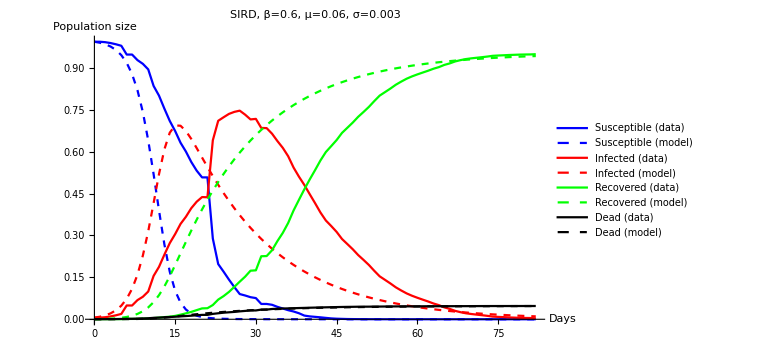

```mathematica
ListLinePlot[{{Range[0,Length[hubei]-1],(hubei⟦-1,1,2⟧-hubei⟦All,1,2⟧)/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv2⟦All,1⟧}ᵀ,{Range[0,Length[hubei]-1],(hubei⟦All,1,2⟧-hubei⟦All,2,2⟧-hubei⟦All,3,2⟧)/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv2⟦All,2⟧}ᵀ,{Range[0,Length[hubei]-1],hubei⟦All,3,2⟧/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv2⟦All,3⟧}ᵀ,{Range[0,Length[hubei]-1],hubei⟦All,2,2⟧/hubei⟦-1,1,2⟧}ᵀ,{Range[0,Length[hubei]-1],hv2⟦All,4⟧}ᵀ},PlotStyle->{Blue,Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed],Black,Directive[Black,Dashed]},PlotLegends->Placed[{"Susceptible (data)","Susceptible (model)","Infected (data)","Infected (model)","Recovered (data)","Recovered (model)","Dead (data)","Dead (model)"},Below],AxesLabel->{"Days","Population size"},PlotLabel->"SIRD, β=0.6, μ=0.06, σ=0.003",ImageSize->Large]
```

### По России

```mathematica
rusdata={Normal[Normal[tsc[Select[#⟦2⟧==Entity["Country","Russia"]&]]]]⟦1,5;;-1,2⟧,Normal[Normal[tsr[Select[#⟦2⟧==Entity["Country","Russia"]&]]]]⟦1,5;;-1,2⟧,Normal[Normal[tsd[Select[#⟦2⟧==Entity["Country","Russia"]&]]]]⟦1,5;;-1,2⟧};
rusdata⟦1⟧=rusdata⟦1⟧-rusdata⟦2⟧-rusdata⟦3⟧;
rusdata=Select[rusdataᵀ,#⟦1⟧>100&]ᵀ;
```

#### s_0=75000

```mathematica
rdv1=N[Prepend[rusdata,75000-Total[rusdata]]/75000];
```

```mathematica
rds0v1=rdv1⟦1,1⟧;
```

```mathematica
rdi0v1=rdv1⟦2,1⟧;
```

```mathematica
rdr0v1=rdv1⟦3,1⟧;
```

```mathematica
rdd0v1=rdv1⟦4,1⟧;
```

```mathematica
rmv1=SIRDi[0.235,0.018,0.00125,rds0v1,rdi0v1,rdr0v1,rdd0v1,200];
```

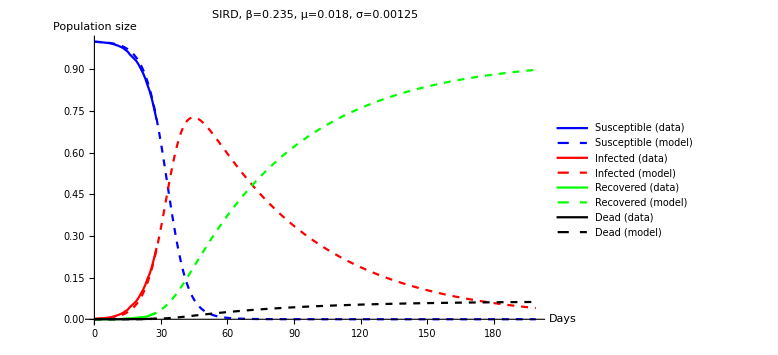

```mathematica
ListLinePlot[{{Range[0,Length[rdv1⟦1⟧]-1],rdv1⟦1⟧}ᵀ,{Range[0,Length[rmv1]-1],rmv1⟦All,1⟧}ᵀ,{Range[0,Length[rdv1⟦1⟧]-1],rdv1⟦2⟧}ᵀ,{Range[0,Length[rmv1]-1],rmv1⟦All,2⟧}ᵀ,{Range[0,Length[rdv1⟦1⟧]-1],rdv1⟦3⟧}ᵀ,{Range[0,Length[rmv1]-1],rmv1⟦All,3⟧}ᵀ,{Range[0,Length[rdv1⟦1⟧]-1],rdv1⟦4⟧}ᵀ,{Range[0,Length[rmv1]-1],rmv1⟦All,4⟧}ᵀ},PlotStyle->{Blue,Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed],Black,Directive[Black,Dashed]},PlotLegends->Placed[{"Susceptible (data)","Susceptible (model)","Infected (data)","Infected (model)","Recovered (data)","Recovered (model)","Dead (data)","Dead (model)"},Below],AxesLabel->{"Days","Population size"},PlotLabel->"SIRD, β=0.235, μ=0.018, σ=0.00125",ImageSize->Large]
```

#### s_0=150000

```mathematica
rdv2=N[Prepend[rusdata,150000-Total[rusdata]]/150000];
```

```mathematica
rds0v2=rdv2⟦1,1⟧;
```

```mathematica
rdi0v2=rdv2⟦2,1⟧;
```

```mathematica
rdr0v2=rdv2⟦3,1⟧;
```

```mathematica
rdd0v2=rdv2⟦4,1⟧;
```

```mathematica
rmv2=SIRDi[0.23,0.02,0.0017,rds0v2,rdi0v2,rdr0v2,rdd0v2,200];
```

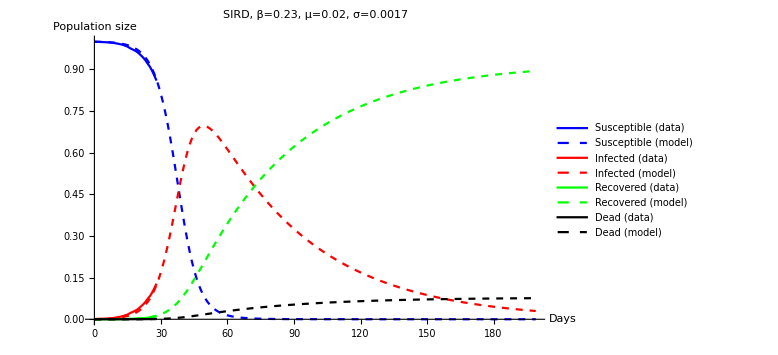

```mathematica
ListLinePlot[{{Range[0,Length[rdv2⟦1⟧]-1],rdv2⟦1⟧}ᵀ,{Range[0,Length[rmv2]-1],rmv2⟦All,1⟧}ᵀ,{Range[0,Length[rdv2⟦1⟧]-1],rdv2⟦2⟧}ᵀ,{Range[0,Length[rmv2]-1],rmv2⟦All,2⟧}ᵀ,{Range[0,Length[rdv2⟦1⟧]-1],rdv2⟦3⟧}ᵀ,{Range[0,Length[rmv2]-1],rmv2⟦All,3⟧}ᵀ,{Range[0,Length[rdv2⟦1⟧]-1],rdv2⟦4⟧}ᵀ,{Range[0,Length[rmv2]-1],rmv2⟦All,4⟧}ᵀ},PlotStyle->{Blue,Directive[Blue,Dashed],Red,Directive[Red,Dashed],Green,Directive[Green,Dashed],Black,Directive[Black,Dashed]},PlotLegends->Placed[{"Susceptible (data)","Susceptible (model)","Infected (data)","Infected (model)","Recovered (data)","Recovered (model)","Dead (data)","Dead (model)"},Below],AxesLabel->{"Days","Population size"},PlotLabel->"SIRD, β=0.23, μ=0.02, σ=0.0017",ImageSize->Large]
```

### Моделирование на основе сети аэропортов

#### Чистка базы данных аэропортов. Остаются только валидные коды IATA

```mathematica
airports=airports[Select[#⟦5⟧=!=""&&StringCases[#⟦5⟧,DigitCharacter..]=={}&]];
```

#### Координаты аэропорта по коду

```mathematica
codecoords=Dispatch[Normal[airports[All,#⟦5⟧->GeoPosition[{#⟦7⟧,#⟦8⟧}]&]]];
```

#### Связи между аэропортами

```mathematica
links=Normal[routes[All,{3,5}]]/.codecoords;
links=Cases[links,{_GeoPosition,_GeoPosition}];
```

#### Визуализация связей между аэропортами. Выбраны 15000 случайных связей

```mathematica
GeoGraphics[{{Red,Opacity[0.3],GeoPath[RandomChoice[links,15000],"Geodesic"]},{FaceForm[],EdgeForm[White],CountryData["Countries","FullPolygon"]}},GeoBackground->None,Background->Black,ImageSize->Large,GeoProjection->"Mercator",GeoRange->{{-65,85},{-180,180}}]
```

-Graphics-

#### Граф на основе связей между аэропортами

```mathematica
g=Graph[UndirectedEdge@@@Union[Sort/@#]]&@Normal[routes[All,{3,5}]];
g=Subgraph[g,First[ConnectedComponents[g]],VertexShapeFunction->"Point",VertexStyle->Directive[Opacity[0.5],Red],EdgeShapeFunction->"Line",EdgeStyle->Directive[Opacity[0.3],White],Background->Black,PerformanceGoal->"Speed"];
```

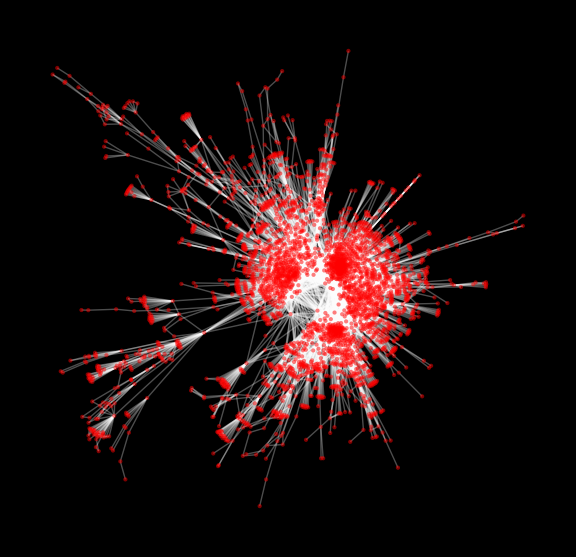

```mathematica
GraphPlot[g,ImageSize->Large]
```

#### Общее количество потенциальных пассажиров в каждом аэропорту

```mathematica
pop=ConstantArray[1., VertexCount[g]];
```

```mathematica
meanNN=AdjacencyMatrix[g].pop;
```

#### Список связных аэропортов для каждого аэропорта

```mathematica
sumind=Flatten[Most[ArrayRules[AdjacencyMatrix[g]⟦#,All⟧]]⟦All,1⟧]&/@Range[VertexCount[g]];
```

#### Параметры модели

```mathematica
ρ=0.2;(*Вероятность заражения*)
```

```mathematica
λ=0.1; (*Вероятность выздоровления*)
```

```mathematica
μ=0.05; (*Коэффициент миграции*)
```

#### Инициализация. Старт с Уханя

```mathematica
{sus[1,#]=1.,inf[1,#]=rec[1,#]=0.}&/@Range[VertexCount[g]];
sus[1,Position[VertexList[g],"WUH"]⟦1,1⟧]=0.95;
inf[1,Position[VertexList[g],"WUH"]⟦1,1⟧]=0.05;
rec[1,Position[VertexList[g],"WUH"]⟦1,1⟧]=0.;
```

#### SIR модель

```mathematica
sus[i_,j_]:=sus[i,j]=(1-μ)(sus[i-1,j]-ρ sus[i-1,j]inf[i-1,j])+μ Total[Table[sus[i-1,sumind⟦j,u⟧]pop⟦sumind⟦j,u⟧⟧,{u,1,Length[sumind⟦j⟧]}]]/meanNN⟦j⟧;
inf[i_,j_]:=inf[i,j]=(1-μ)(inf[i-1,j]+ρ sus[i-1,j]inf[i-1,j]-λ inf[i-1,j])+μ Total[Table[inf[i-1,sumind⟦j,u⟧]pop⟦sumind⟦j,u⟧⟧,{u,1,Length[sumind⟦j⟧]}]]/meanNN⟦j⟧;
rec[i_,j_]:=rec[i,j]=(1-μ)(rec[i-1,j]+λ inf[i-1,j])+μ Total[Table[rec[i-1,sumind⟦j,u⟧]pop⟦sumind⟦j,u⟧⟧,{u,1,Length[sumind⟦j⟧]}]]/meanNN⟦j⟧;
```

#### Моделирование

```mathematica
tcourse=ParallelTable[{sus[i,j],inf[i,j],rec[i,j]},{i,1,300},{j,1,VertexCount[g]}];
```

#### SIR кривые для 200 случайных аэропортов

```mathematica
ListLinePlot[Flatten[Table[{tcourse⟦All,j,1⟧,tcourse⟦All,j,2⟧,tcourse⟦All,j,3⟧},{j,RandomSample[Range[VertexCount[g]],200]}],1],PlotTheme->"Detailed",PlotRange->All,PlotStyle->Opacity[0.5],ImageSize->Large]
```

-Graphics-

#### Максимальная доля больных среди всех аэропортов

```mathematica
maxsick=Max[tcourse⟦All,All,2⟧];
```

#### Координаты аэропортов

```mathematica
airportcoords=VertexList[g]/.codecoords;
```

#### Карта заражения в зависимости от времени

```mathematica
TableForm@ParallelTable[GeoRegionValuePlot[Thread[airportcoords->tcourse⟦k,All,2⟧/maxsick],ColorFunction->"Rainbow",ImageSize->Large,PlotStyle->AbsolutePointSize[3],PlotLegends->None],{k,{50,75,100,125,150,175,200,225}}]
```

-Graphics-